```mathematica
Clear[x,y,z,s,xp,yp]
l={{-xp,(s/2)*b,0},{(-s/2),-yp,0},{xp,(-s/2)*b,0},{(s/2),yp,0}};
b:=1/2;
dl={{-1,0,0},{0,-1,0},{1,0,0},{0,1,0}};
R1={x,y,z}-l[[1]]
R2={x,y,z}-l[[2]]
R3={x,y,z}-l[[3]]
R4={x,y,z}-l[[4]]
mod1=Sqrt[R1.R1];
mod2=Sqrt[R2.R2];
mod3=Sqrt[R3.R3];
mod4=Sqrt[R4.R4];
c1=Cross[dl[[1]],R1];
c2=Cross[dl[[2]],R2];
c3=Cross[dl[[3]],R3];
c4=Cross[dl[[4]],R4];
inte1=c1/(mod1^3);
inte2=c2/(mod2^3);
inte3=c3/(mod3^3);
inte4=c4/(mod4^3);
intex=inte1[[1]]+inte2[[1]]+inte3[[1]]+inte4[[1]]
intey=inte1[[2]]+inte2[[2]]+inte3[[2]]+inte4[[2]]
intez=inte1[[3]]+inte2[[3]]+inte3[[3]]+inte4[[3]]
{xp,yp}:={ep,ep*b};
Bz=Assuming[0.03>s>0&&z>0&&-2s<x<2s&&-2s<y<2s,Integrate[intez,{ep,-s/2,s/2}]]
Bx=Assuming[0.03>s>0&&0.02>z>0&&-2s<x<2s&&-2s<y<2s,Integrate[intex,{ep,-s/2,s/2}]]
By=Assuming[0.03>s>0&&0.02>z>0&&-2s<y<2s&&-2s<x<2s,Integrate[intey,{ep,-s/2,s/2}]]
```

{x+xp,-s/4+y,z}

{s/2+x,y+yp,z}

{x-xp,s/4+y,z}

{-s/2+x,y-yp,z}

z/(((-s/2+x)^2+(y-yp)^2+z^2)^(3/2))-z/(((s/2+x)^2+(y+yp)^2+z^2)^(3/2))

z/(((x+xp)^2+(-s/4+y)^2+z^2)^(3/2))-z/(((x-xp)^2+(s/4+y)^2+z^2)^(3/2))

(s/4-y)/(((x+xp)^2+(-s/4+y)^2+z^2)^(3/2))+(s/4+y)/(((x-xp)^2+(s/4+y)^2+z^2)^(3/2))+(s/2-x)/(((-s/2+x)^2+(y-yp)^2+z^2)^(3/2))+(s/2+x)/(((s/2+x)^2+(y+yp)^2+z^2)^(3/2))

(8 (s-4 y) (2 x (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))-1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s-4 y)^2+16 z^2)+(4 (s-2 x) (4 y (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))-1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s-2 x)^2+4 z^2)+(8 (s/2+x) (4 y (-1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s+2 x)^2+4 z^2)+(32 (s/4+y) (2 x (-1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s+4 y)^2+16 z^2)

(8 z (4 y (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))-1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s-2 x)^2+4 z^2)-(8 z (4 y (-1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s+2 x)^2+4 z^2)

(32 z (2 x (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))-1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (2 x-y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2-8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s-4 y)^2+16 z^2)-(32 z (2 x (-1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))+s (1/(√(5 s^2+8 s (-2 x+y)+16 (x^2+y^2+z^2)))+1/(√(5 s^2+8 s (2 x+y)+16 (x^2+y^2+z^2))))))/((s+4 y)^2+16 z^2)

```mathematica
z=3*10^(-3);
s=Table[s,{s,2,16,2}]*10^(-3);
s
Plot3D[(Sqrt[((Norm[0.1*Bx[[1;;8]]]^2 )+(Norm[0.1*Bz[[1;;8]]]^2)+(Norm[0.1*By[[1;;8]]]^2))]),{x,-0.010,0.010},{y,-0.010,0.010},ColorFunction->Function[{x,y,z},Hue[0.65(1-z)]],Mesh->40,AxesLabel->{"x-coordinate (m)","y-coordinate (m)","B field (μT)
per unit 
current"},PlotRange->All]
```

{1/500,1/250,3/500,1/125,1/100,3/250,7/500,2/125}

-Graphics3D-

```mathematica
z=3*10^(-3);
plots[i_]:= Plot3D[(Sqrt[((Norm[0.1*Bx]^2 )+(Norm[0.1*Bz]^2)+(Norm[0.1*By]^2))]),{x,-0.010,0.010},{y,-0.010,0.010},ColorFunction->Function[{x,y,z},Hue[0.65(1-z)]],Mesh->40,AxesLabel->{"x-coordinate (m)","y-coordinate (m)","B field (μT)
per unit 
current"},PlotRange->All]
Do[Print[plots[s]],{s,2*10^(-3),20*10^(-3),2*10^(-3)}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«7 more identical outputs»

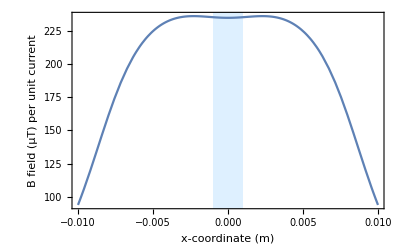

```mathematica
y=0;
Plot[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1Bz]^2))]),{x,-0.01,0.01},Prolog->{LightBlue,Rectangle[{-0.0010,-1000},{0.0010,10000}]},Frame->True,FrameLabel->{"x-coordinate (m)","B field (μT) per unit current"}]
```

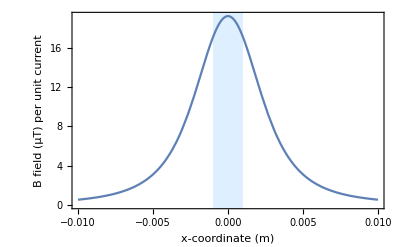

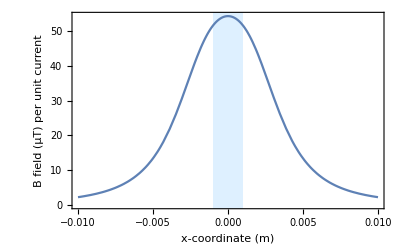

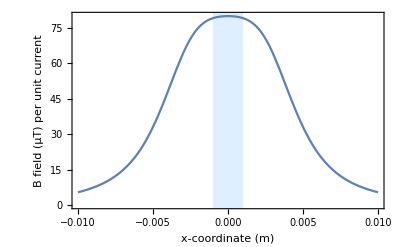

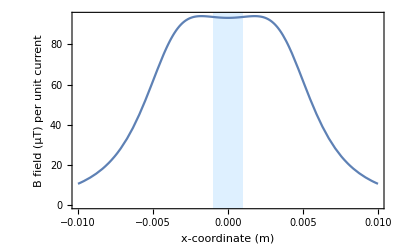

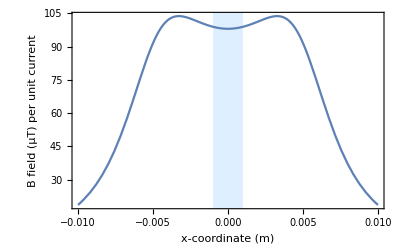

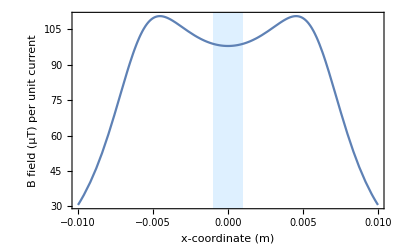

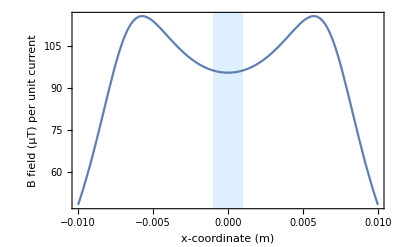

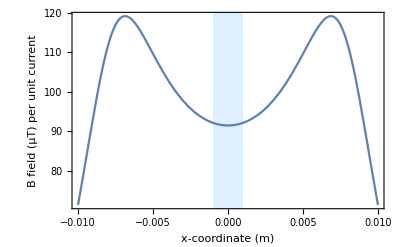

```mathematica
y=0;
plotties[j_]:=Plot[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1Bz]^2))]),{x,-0.01,0.01},Prolog->{LightBlue,Rectangle[{-0.0010,-1000},{0.0010,10000}]},Frame->True,FrameLabel->{"x-coordinate (m)","B field (μT) per unit current"}]
Do[Print[plotties[s]],{s,2*10^(-3),20*10^(-3),2*10^(-3)}]
```

```mathematica
(*curve[k_]=(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1Bz]^2))]);
s=Table[s,{s,2,20,2}]*10^(-3);
field:=Do[Print[NIntegrate[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1Bz]^2))]),{x,-0.001,0.001}]],{s,2*10^(-3),20*10^(-3),2*10^(-3)}]
field*)
```

```mathematica
fieldt:=Table[NIntegrate[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1By]^2)+(Norm[0.1Bz]^2))]),{x,-0.001,0.001},{y,-0.00045,0.00045}],{s,2*10^(-3),20*10^(-3),2*10^(-3)}]
fieldt
```

{0.0000328912,0.0000951574,0.00014257,0.00016742,0.000176561,0.000176667,0.000171983,0.000164967,0.000156997,0.000148831}

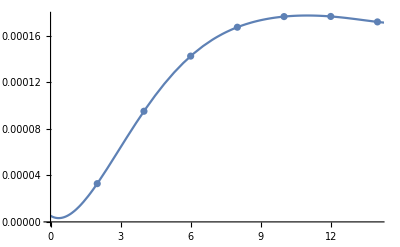

```mathematica
fieldt;
s;
combine=Riffle[(s*1000),fieldt];
combined=Partition[combine,2];
(*ListPlot[combined]*)

polifit=Fit[combined,{1,a,a^2,a^3,a^4,a^5,a^6},a];

Show[ListPlot[combined],Plot[polifit,{a,0,20}]]
```

```mathematica
s=7.08486*10^(-3);
oi=NIntegrate[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1By]^2)+(Norm[0.1Bz]^2))]),{x,-0.001,0.001},{y,-0.00045,0.00045}]
optifield={{s*10^3,oi}}
```

0.000158482

{{7.08486,0.000158482}}

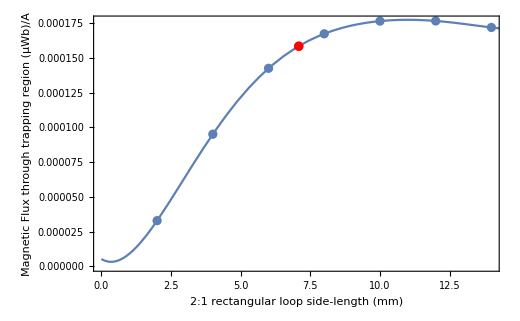

```mathematica
Show[ListPlot[combined],Plot[polifit,{a,0,20}],ListPlot[optifield,PlotStyle->Red],Frame->True,FrameLabel->{"2:1 rectangular loop side-length (mm)","Magnetic Flux through trapping region (μWb)/A"}]
```

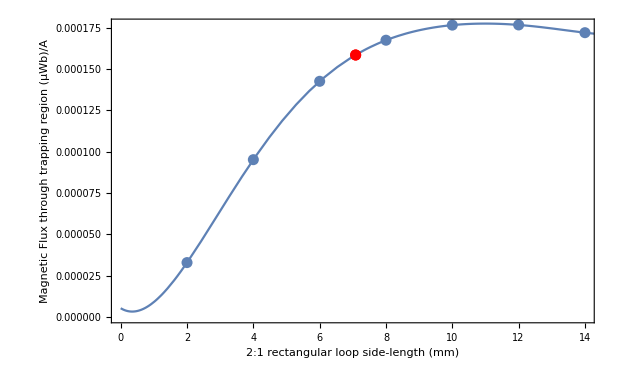

```mathematica
max=FindMaximum[polifit,a]
```

{0.00017748,{a→10.9935}}

```mathematica
Bavg=(max[[1]])/(2*10^(-3)*0.9*10^(-3))
```

98.6003

```mathematica
optifield[[1,2]]
max[[1]]
increase=max[[1]]/optifield[[1,2]]
percen=increase*100-100
```

0.000158482

0.00017748

1.11988

11.9879